```mathematica
(*Define the f function, also for zero values*)
```

```mathematica
f[x_,y_,sigma_]:=Erf[Abs[x-y]/(2*sigma)]/Abs[x-y]
```

```mathematica
f[x_,x_,sigma_]:=1/(sigma*Sqrt[Pi])
```

```mathematica
(*Expression for g(x,y), assuming two particles of masses m[[0]], m[[1]]*)
g[x_,y_, m_, sigma_]:=Sum[m[[j]]*m[[k]]*((I-1)*f[x[[j]],x[[k]],sigma]+(-I-1)*f[y[[j]],y[[k]], sigma]+2*f[x[[j]],y[[k]],sigma]),{j,1,2},{k,1,2}]
```

```mathematica
(*module to create a two-dimensional vector in the computational basis*)
```

```mathematica
Vect2[l_]:=Module[{v},
v=ConstantArray[0,{2,1}];
v[[l]]={1};
v]
```

```mathematica
(*code to generate the qubit projectors |l><l|*)
```

```mathematica
Proj2[l_]:=Module[{P},
P=ConstantArray[0,{2,2}];
P[[l]][[l]]=1;
P]
```

```mathematica
(*Code to generate A in superoperator form, i.e. A=\sum_{x,y}g(x,y)|x><x|\otimes |y><y|. The two position values for the first (second) particle are encooded in the entries of s (t) *)
```

```mathematica
Lindblad[s_,t_, m_,sigma_]:=Module[{},
Sum[KroneckerProduct[Proj2[j1],Proj2[j2],Proj2[k1],Proj2[k2]]*g[{s[[j1]],t[[j2]]},{s[[k1]],t[[k2]]}, {m[[1]],m[[2]]}, sigma],{j1,1,2},{j2,1,2},{k1,1,2},{k2,1,2}]
]
```

```mathematica
(*define A (in superoperator form) for the position vectors a^1, a^2, b^1, b^2 in the main text*)
```

```mathematica
A=Lindblad[{0,L},{d+L,d+2*L},{m,m},sigma];
```

```mathematica
(*states: pure and mixed*)
```

```mathematica
(*|+>^{\otimes 2}*)
```

```mathematica
vPlus={{1},{1},{1},{1}}/2;
```

```mathematica
(*|->^{\otimes 2}*)
```

```mathematica
vMinus={{1},{-1},{-1},{1}}/2;
```

```mathematica
(*\rho_0=|+><+|^{\otimes 2}: *)
rho0=vPlus.Transpose[vPlus]
```

{{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4}}

```mathematica
(*A acting on \rho_0*)
```

```mathematica
Arho0=ArrayReshape[A.ArrayReshape[rho0,{16,1}],{4,4}];
```

```mathematica
(*partial transposition of a two-qubit state*)
PartialTranspose[rho_]:=Sum[KroneckerProduct[IdentityMatrix[2],Vect2[j].Transpose[Vect2[k]]].rho.KroneckerProduct[IdentityMatrix[2],Vect2[j].Transpose[Vect2[k]]],{k,1,2},{j,1,2}]
```

```mathematica
(*compute the matrix (1-|+><+|^{\otimes 2})A(rho_0)(1-|+><+|^{\otimes 2})*)
```

```mathematica
specialMatrix=(IdentityMatrix[4]-rho0).PartialTranspose[Arho0].(IdentityMatrix[4]-rho0);
```

```mathematica
eige=Simplify[Eigenvalues[specialMatrix]]
```

{0,0,-(m^2 (-2 Abs[d] Abs[L] Abs[d+L] Abs[d+2 L]+2 √π sigma Abs[d] Abs[d+L] Abs[d+2 L] Erf[Abs[L]/(2 sigma)]+√(2 π) Abs[L] √(sigma^2 (-2 Abs[d] Abs[d+2 L] Erf[Abs[d+L]/(2 sigma)]+Abs[d+L] (Abs[d+2 L] Erf[Abs[d]/(2 sigma)]+Abs[d] Erf[Abs[d+2 L]/(2 sigma)]))^2)))/(2 √π sigma Abs[d] Abs[L] Abs[d+L] Abs[d+2 L]),(m^2 (2 Abs[d] Abs[L] Abs[d+L] Abs[d+2 L]-2 √π sigma Abs[d] Abs[d+L] Abs[d+2 L] Erf[Abs[L]/(2 sigma)]+√(2 π) Abs[L] √(sigma^2 (-2 Abs[d] Abs[d+2 L] Erf[Abs[d+L]/(2 sigma)]+Abs[d+L] (Abs[d+2 L] Erf[Abs[d]/(2 sigma)]+Abs[d] Erf[Abs[d+2 L]/(2 sigma)]))^2)))/(2 √π sigma Abs[d] Abs[L] Abs[d+L] Abs[d+2 L])}

```mathematica
(*We verify if those complicated expressions correspond to the terms E_{\pm} in the paper (note that we omit the pre-fadctor G/2\hbar)*)
```

```mathematica
EPlus[d_,L_,m_,sigma_]:=m^2*(1/(Sqrt[Pi]*sigma)-f[L,0, sigma]+(1/Sqrt[2])*Abs[f[d+2*L,0, sigma]+f[d,0, sigma]-2*f[d+L,0, sigma]])
```

```mathematica
EMinus[d_,L_,m_,sigma_]:=m^2*(1/(Sqrt[Pi]*sigma)-f[L,0, sigma]-(1/Sqrt[2])*Abs[f[d+2*L,0, sigma]+f[d,0, sigma]-2*f[d+L,0, sigma]])
```

```mathematica
Simplify[eige[[3]]-EMinus[d,L,m,sigma],Assumptions->{Element[sigma, Reals],sigma>0}]
```

0

```mathematica
Simplify[eige[[4]]-EPlus[d,L,m,sigma],Assumptions->{Element[sigma, Reals],sigma>0}]
```

0

```mathematica
(*confirmed*)
(*We next verify that one of the zero eigenvalues of the matrix has eigenvector |- >^{\otimes 2}*)
```

```mathematica
Simplify[specialMatrix.vMinus]
```

{{0},{0},{0},{0}}

```mathematica
(*second order perturbation theory*)
(*First, compute the matrix element <phi_0|A(rho_0)^{T_1}|phi_3>*)
overlapPlusMin=Simplify[Transpose[vPlus].PartialTranspose[Arho0].vMinus][[1,1]]
```

1/2 m^2 (-Erf[Abs[d]/(2 sigma)]/Abs[d]+(2 Erf[Abs[d+L]/(2 sigma)])/Abs[d+L]-Erf[Abs[d+2 L]/(2 sigma)]/Abs[d+2 L])

```mathematica
(*Next, compute <phi_3|A^2(rho_0)|phi_3>*)
```

```mathematica
A2rho0=ArrayReshape[A.A.ArrayReshape[rho0,{16,1}],{4,4}];
```

```mathematica
overlapMinMin=Simplify[Transpose[vMinus].PartialTranspose[A2rho0].vMinus][[1,1]]
```

1/2 m^4 (4/(π sigma^2)+(3 Erf[Abs[d]/(2 sigma)]^2)/Abs[d]^2-(8 Erf[Abs[L]/(2 sigma)])/(√π sigma Abs[L])+(4 Erf[Abs[L]/(2 sigma)]^2)/Abs[L]^2+(12 Erf[Abs[d+L]/(2 sigma)]^2)/Abs[d+L]^2-(12 Erf[Abs[d+L]/(2 sigma)] Erf[Abs[d+2 L]/(2 sigma)])/(Abs[d+L] Abs[d+2 L])+(3 Erf[Abs[d+2 L]/(2 sigma)]^2)/Abs[d+2 L]^2+(6 Erf[Abs[d]/(2 sigma)] (-2 Abs[d+2 L] Erf[Abs[d+L]/(2 sigma)]+Abs[d+L] Erf[Abs[d+2 L]/(2 sigma)]))/(Abs[d] Abs[d+L] Abs[d+2 L]))

```mathematica
(*second order eigenvalue for |\phi_3> (remember that we are omiting the pre-factor (G/2\hbar)^2*)
```

```mathematica
lambda3=Simplify[overlapMinMin-2*overlapPlusMin^2]
```

m^4 (2/(π sigma^2)+Erf[Abs[d]/(2 sigma)]^2/Abs[d]^2-(4 Erf[Abs[L]/(2 sigma)])/(√π sigma Abs[L])+(2 Erf[Abs[L]/(2 sigma)]^2)/Abs[L]^2+(4 Erf[Abs[d+L]/(2 sigma)]^2)/Abs[d+L]^2-(4 Erf[Abs[d+L]/(2 sigma)] Erf[Abs[d+2 L]/(2 sigma)])/(Abs[d+L] Abs[d+2 L])+Erf[Abs[d+2 L]/(2 sigma)]^2/Abs[d+2 L]^2+(2 Erf[Abs[d]/(2 sigma)] (-2 Abs[d+2 L] Erf[Abs[d+L]/(2 sigma)]+Abs[d+L] Erf[Abs[d+2 L]/(2 sigma)]))/(Abs[d] Abs[d+L] Abs[d+2 L]))

```mathematica
(*verify if this complicated expression ca be written more succintly*)
lambda3Simple=m^4*(2*(1/(Sqrt[Pi]*sigma)-f[L,0,sigma])^2+(f[d,0,sigma]+f[2*L+d,0,sigma]-2*f[L+d,0,sigma])^2)
```

m^4 (2 (1/(√π sigma)-Erf[Abs[L]/(2 sigma)]/Abs[L])^2+(Erf[Abs[d]/(2 sigma)]/Abs[d]-(2 Erf[Abs[d+L]/(2 sigma)])/Abs[d+L]+Erf[Abs[d+2 L]/(2 sigma)]/Abs[d+2 L])^2)

```mathematica
Simplify[lambda3-lambda3Simple]
```

0

```mathematica
(*explore for which values of L EMinus is negative for greater distances d (since the value of sigma just rescales the graph, we take sigma=1)*)
```

```mathematica
maxDist[L_]:=FindRoot[EMinus[d,L,1,1],{d,1}][[1,2]]
```

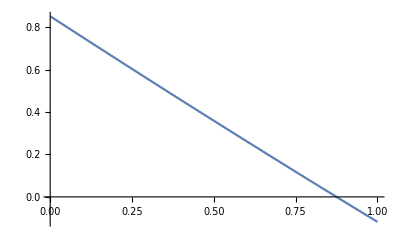

```mathematica
Plot[maxDist[L],{L,0.001,1}]
```

```mathematica
(*Low values of L allow a greater positive) distance between the particles*)
```

```mathematica
(*Find maximum distance*)
```

```mathematica
(*compute double differential of \tilde{f}(d)*)
```

```mathematica
f2[d_]:=Simplify[D[D[Erf[d/2]/d,d],d]]
```

```mathematica
(*define \gamma funciton as in the main text*)
```

```mathematica
gamma[d_]:=(-1/2)*Limit[f2[s],{s->0}]-Abs[f2[d]]/Sqrt[2]
```

```mathematica
FindRoot[gamma[d],{d,1}]
```

{d→0.850872}

```mathematica
(*re-scaling, we have that d_c=0.850872\sigma*)
```